```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
c=299792.458"km"/"s";
AutoPlotRegends[params_List]:=ToString[#/.Rule[a_,b_]:>ToString[a]<>"="<>ToString[b]]//.x_List:>StringJoin[Riffle[x,", "]]&/@params
```

```mathematica
(* distance modules *)
μ[z_,Ωm_,H0_]:=25+5Log10[DL[z,Ωm,H0]/("Mpc")]
(* luminosity distance *)
DL[z_,Ωm_,H0_]:=c/H0(1+z)(η[1,Ωm]-η[1/(1+z),Ωm])
η[a_,Ωm_]:=Module[{s=((1-Ωm)/Ωm)^(1/3)},
2 √(s^3+1)(1/a^4-0.1540 s/a^3+0.4304 s^2/a^2+0.19097 s^3/a+0.066941 s^4)^(-1/8)]
```

#### Problem 1

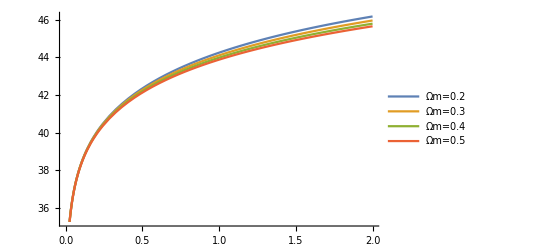

```mathematica
ListΩm={Ωm->0.2,Ωm->0.3,Ωm->0.4,Ωm->0.5};
TheoryPlot=Plot[μ[z,Ωm,70("km")/("s""Mpc")]/.#&/@ListΩm//Evaluate,{z,0,2},PlotLegends->AutoPlotRegends[ListΩm]]
```

#### Problem 2

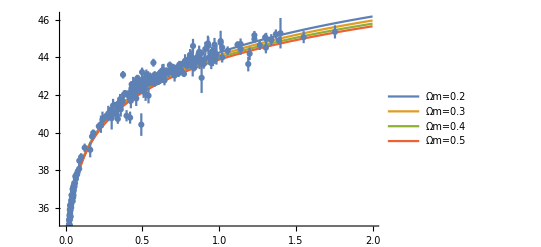

```mathematica
Data=Select[Import["SN.txt","Table"],Length[#]==5&][[2;;]];
DataPlot=ErrorListPlot[{{#[[2]],#[[3]]},ErrorBar[#[[4]]]}&/@Data];
Show[{TheoryPlot,DataPlot}]
```

#### Problem 3

```mathematica
RandomSupernova[z_,Ωm_,H0_,σ_]:=RandomVariate[NormalDistribution[μ[z,Ωm,70("km")/("s""Mpc")],0.1]]
PseudoSupernovae={#,RandomSupernova[#,0.3,70("km")/("s""Mpc"),0.1]}&/@RandomReal[{0,2},20]
```

{{0.93304,43.9771},{0.495199,42.2795},{1.0617,44.0842},{1.18258,44.5053},{0.147255,39.1825},{0.283571,40.8677},{1.34246,45.0498},{1.34641,44.9452},{0.538125,42.5795},{0.703081,42.9668},{1.8756,45.9433},{0.0237469,35.0752},{0.409119,41.8036},{0.445086,41.9122},{1.3344,44.9988},{1.61284,45.4026},{0.179802,39.7017},{1.32336,44.8565},{0.151601,39.348},{0.576514,42.7675}}

#### Problem 4

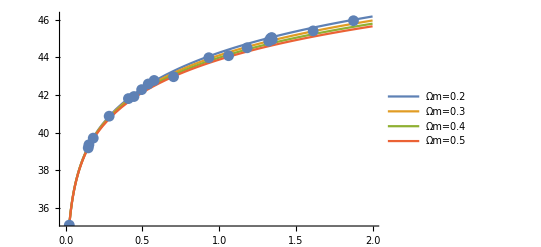

```mathematica
PseudoDataPlot=ErrorListPlot[{{#[[1]],#[[2]]},ErrorBar[0.1]}&/@PseudoSupernovae];
Show[{TheoryPlot,PseudoDataPlot}]
```

#### Problem 5

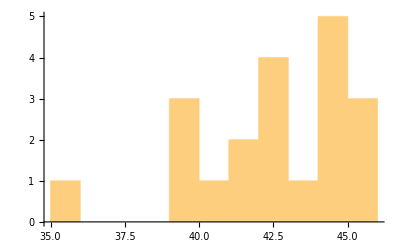

```mathematica
Histogram[PseudoSupernovae[[All,2]],{1}]
```